```mathematica
Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;
```

```mathematica
(* 9-j symbol ({{j1, j2, j12}, {j3, j4, j34}, {j13, j24, j}})*)
NineJSymbol[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,j_}]:=Simplify[Sum[(-1)^(2g)(2g+1)SixJSymbol[{j1,j2,j12},{j34,j,g}]SixJSymbol[{j3,j4,j34},{j2,g,j24}]SixJSymbol[{j13,j24,j},{g,j1,j3}],{g,Max[Abs[j1-j],Abs[j2-j34],Abs[j3-j24]],Min[j1+j,j2+j34,j3+j24],1-Mod[2*(j1+j),2]/2}]]
```

```mathematica
(* Indexing of states *)
Nmax=12;imax=0;
Clear[i,j];
i=0;
For[NShell=0,NShell≤Nmax,NShell++,
For[n=0,2n≤NShell,++n,
For[s=0,s≤1,++s,
For[l=0,2n+l≤NShell,++l,
For[j=Abs[l-s],j≤l+s,j++,
For[N0=0,2(N0+n)+l≤NShell,++N0,
L=NShell-2(N0+n)-l;
For[J0=Abs[L-j],J0≤L+j,J0++,
For[Jz=-J0,Jz≤J0,Jz++,
If[EvenQ[l+s]&&L≥0&&2(N0+ n)+l+L≤NShell&&Abs[L-j]≤J0≤Abs[L+j],imax+=1;i+=1;
Ni[i]=N0;ni[i]=n;si[i]=s;li[i]=l;Li[i]=L;ji[i]=j;Ji[i]=J0;Jzi[i]=Jz;
(*Print["N_shell=",2(N0+n)+L+l,"   |",i,">=|",n,"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,Jz,">"];*)
(*Print["N_shell=",2(N0+n)+L+l];*)
]]]]]]]]]
Clear[i,l,L,N0,n,s,j,J0,Jz,NShell];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 37044 included states.

```mathematica
(* Indexing of states *)
i=0;imax=0;
For[NShell=0,NShell≤Nmax,NShell++,
For[n=0,2n≤NShell,++n,
For[s=0,s≤1,++s,
For[l=0,2n+l≤NShell,++l,
For[j=Abs[l-s],j≤l+s,j++,
For[N0=0,2(N0+n)+l≤NShell,++N0,
L=NShell-2(N0+n)-l;
For[J0=Abs[L-j],J0≤L+j,J0++,
For[Jz=0,Jz≤0,Jz++,
If[EvenQ[l+s]&&L≥0&&2(N0+ n)+l+L≤NShell&&Abs[L-j]≤J0≤Abs[L+j],imax+=1;i+=1;
Ni[i]=N0;ni[i]=n;si[i]=s;li[i]=l;Li[i]=L;ji[i]=j;Ji[i]=J0;Jzi[i]=Jz;
(*Print["N_shell=",2(N0+n)+L+l,"   |",i,">=|",n,"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,Jz,">"];*)
(*Print["N_shell=",2(N0+n)+L+l];*)
]]]]]]]]]
Clear[i,l,L,N0,n,s,j,J0,Jz,NShell];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 3612 included states.

```mathematica
(* Precompute the 3j symbols *)
Clear[JThree];
temp=0;
Timing[
For[J=0,J≤Nmax+1,++J,
For[J1=Max[0,J-1],J1≤J+1,++J1,
For[Jz=-J,Jz≤J&&Jz≤J1,Jz++,
If[!NumericQ[JThree[J1,-Jz,1,0,J,Jz]],temp++;JThree[J1,-Jz,1,0,J,Jz]=ThreeJSymbol[{J1,-Jz},{1,0},{J,Jz}];
] (* If NumericQ *)
](* Jz *)
] (* J1 *)
];(* J *)
] (* Timing *)
temp
Clear[J,J1,Jz,temp];
```

{0.56686,Null}

574

```mathematica
(* Precompute the 6j symbols *)
(* Need to impose Δj≤1,ΔJ≤1 *)
Clear[JSix];
temp=0;
Timing[
For[j=0,j≤Nmax,j++,
For[j1=Abs[1-j],j1≤j+1,j1++,
For[L=0,L≤Nmax-j+1,L++,
For[J=Abs[L-j],J≤L+j,J++,
For[J1=Abs[L-j1],J1≤L+j1,J1++,
If[Abs[J-J1]≤1≤Abs[J+J1],
If[!NumericQ[JSix[j1,J1,L,J,j,1]],temp++;JSix[j1,J1,L,J,j,1]=SixJSymbol[{j1,J1,L},{J,j,1}];
] (* If NumericQ *)
] (* If Abs[J-J1] *)
](* J1 *)
] (* J *)
] (* L *)
](* j1 *)
];(* j *)
] (* Timing *)
temp
Clear[j,j1,L,J,J1,temp];
```

{8.34789,Null}

3784

```mathematica
(* Not enforcing triangular inequality on l+J0,J *)
temp=0;
Timing[
For[l=0,l≤Nmax,l++,
For[L=0,L≤Nmax-l,L++,
For[j=Abs[l-1],j≤l+1,j++,
For[J=Abs[j-L],J≤j+L,J++,
For[J0=Abs[L-1],J0≤L+1,J0++,
If[(*Abs[J0-l]≤J≤J0+l&&*)Abs[j-L]≤J≤j+L,
If[!NumericQ[JSix[l,1,j,L,J,J0]],temp++;JSix[l,1,j,L,J,J0]=SixJSymbol[{l,1,j},{L,J,J0}];
] (* If NumericQ *)
](* If Abs *)
](* J0 *)
] (* L *)
] (* J *)
](* j *)
];(* l *)
] (* Timing *)
temp
Clear[l,j,J,L,J0,temp];
```

{7.33276,Null}

3484

```mathematica
(* Need to impose ΔJ0≤1,ΔJ≤1 *)
temp=0;
Timing[
For[l=0,l≤Nmax,l++,
For[J0=0,J0≤Nmax+1,J0++,
For[J01=0,J01≤Nmax+1,J01++,
For[J=Abs[J0-l],J≤J0+l,J++,
For[J1=Abs[J01-l],J1≤Nmax+1,J1++,
If[Abs[J-1]≤J1≤J+1&&Abs[J0-1]≤J01≤J0+1,
If[!NumericQ[JSix[J01,J1,l,J,J0,1]],temp++;JSix[J01,J1,l,J,J0,1]=SixJSymbol[{J01,J1,l},{J,J0,1}];
] (* If NumericQ *)
](* If Abs *)
](* J01 *)
] (* J0 *)
] (* J1 *)
](* J *)
] ;(* l *)
] (* Timing *)
temp
Clear[l,J,J1,J0,J01,temp];
```

{16.23519,Null}

6549

```mathematica
(* Precompute the 9j Symbols *)
(* Assuming L=L' \pm 1 *)
Clear[JNine];
temp=0;
Timing[
For[L=0,L≤Nmax,L++,
For[L1=0,L1≤Nmax,L1++,
For[J0=Abs[L-1],J0≤L+1,J0++,
For[J01=Abs[L1-1],J01≤L1+1,J01++,
If[Abs[L-L1]==1&&Abs[J0-J01]≤1≤J0+J01,
If[L1==1&&L==0&&J01==1&&J0==0,Print["TEST"]];
If[!NumericQ[JNine[L1,L,1,1,1,1,J01,J0,1]],temp++;JNine[L1,L,1,1,1,1,J01,J0,1]=NineJSymbol[{L1,L,1},{1,1,1},{J01,J0,1}];
] (* If NumericQ *)
](* If Abs *)
](* J01 *)
] (* J0 *)
] (* L1 *)
];(* L *)
] (* Timing *)
temp
Clear[L,L1,J0,J01,temp];
```

{1.58512,Null}

138

```mathematica
temp=0;
Timing[
For[l=0,l≤Nmax,l++,
For[l1=0,l1≤Nmax,l1++,
For[s=0,s≤1,s++,
s1=Abs[1-s];
If[EvenQ[l+s]&&EvenQ[l1+s1],
For[j=Abs[l-s],j≤l+s,j++,
For[j1=Abs[l1-s1],j1≤l1+s1,j1++,If[Abs[l-l1]==1&&Abs[j-j1]≤1≤j+j1,
If[!NumericQ[JNine[l1,l,1,s1,s,1,j1,j,1]],temp++;JNine[l1,l,1,s1,s,1,j1,j,1]=NineJSymbol[{l1,l,1},{s1,s,1},{j1,j,1}];
] (* If NumericQ *);
](* If Abs *)
](* j1 *)
] (* j *)
] (* If EvenQ *)
] (* s *)
] (* l1 *)
];(* l *)
] (* Timing *)
temp
Clear[l,l1,s,s1,j,j1,temp];
```

{0.43018,Null}

46

```mathematica
(* This is the actual reduced matrix element of q *)
q[n1_,l1_,n_,l_]:= If[Abs[l1-l]==1,(I (-1)^(l1+1))/ThreeJSymbol[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3/2]Gamma[n1+l1+3/2])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3/2]Gamma[m1+l1+3/2])Which[l1==l+1,(l+1)/Sqrt[(2l+1)(2l+3)] (2m Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),l1==l-1,l/Sqrt[(2l+1)(2l-1)]((2m+2l+1) Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),True,0],{m,0,n},{m1,0,n1}],0];
```

```mathematica
σq[n1_,s1_,l1_,j1_,L1_,J1_,J1z_,n_,s_,l_,j_,L_,J_,Jz_]:= 6α I Sqrt[(2J+1)(2J1+1)(2j+1)(2j1+1)](-1)^(J+J1-J1z+j1+L+1)JThree[J1,-J1z,1,0,J,Jz]JSix[j1,J1,L,J,j,1]JNine[l1,l,1,s1,s,1,j1,j,1]q[n1,l1,n,l](s1-s)

ΣQ[l1_,s1_,j1_,N1_,L1_,J1_,J1z_,l_,s_,j_,N_,L_,J_,Jz_]:=
6Sqrt[2]α I Sqrt[(2j+1)(2j1+1)(2J+1)(2J1+1)](-1)^(J+J1-J1z+l)JThree[J1,-J1z,1,0,J,Jz]q[N1,L1,N,L]Sum[(-1)^J2(2J2+1)(2J21+1)JSix[l,1,j,L,J,J2]JSix[l1,1,j1,L1,J1,J21]JSix[J21,J1,l,J,J2,1]JNine[L1,L,1,1,1,1,J21,J2,1],{J2,Abs[L-s],Abs[L+s]},{J21,Max[Abs[L1-s1],J2-1],Min[Abs[L1+s1],J2+1]}](KroneckerDelta[s,1]KroneckerDelta[s1,1])
```

```mathematica
H[n1_,l1_,s1_,j1_, N1_,L1_,J1_,J1z_,n_,l_,s_,j_, N_,L_,J_,Jz_]:=If[J1z==Jz&&Abs[J-J1]≤1≤J+J1,If[N==N1&&L==L1&&Abs[l-l1]==1&&Abs[s-s1]==1&&Abs[j-j1]≤1≤j+j1,
σq[n1,s1,l1,j1,L1,J1,J1z,n,s,l,j,L,J,Jz],0]+If[n==n1&&l==l1&&s1==s&&s==1&&Abs[L-L1]==1,ΣQ[l1,s1,j1,N1,L1,J1,J1z,l,s,j,N,L,J,Jz],0],0]
```

```mathematica
(*H0=Table[H[ni[i],li[i],si[i],ji[i],Ni[i],Li[i],Ji[i],Jzi[i],ni[j],li[j],si[j],ji[j],Ni[j],Li[j],Ji[j],Jzi[j]],{i,1,imax},{j,1,imax}];

H0//MatrixForm//FullSimplify
HermitianMatrixQ[ReplaceAll[H0,α->1]]*)
```

```mathematica
Timing[H0=Table[0,{i,1,imax},{j,1,imax}];
For[i=1,i≤imax,++i,
If[i/100∈Integers,Print[i]];
For[j=1,j<i,j++,H0[[i,j]]=H[ni[i],li[i],si[i],ji[i],Ni[i],Li[i],Ji[i],Jzi[i],ni[j],li[j],si[j],ji[j],Ni[j],Li[j],Ji[j],Jzi[j]]]]
Assuming[α∈Reals,H0=H0+α Transpose[Conjugate[H0/α]]];H0=H0+DiagonalMatrix[Table[2ni[i]+2Ni[i]+li[i]+Li[i]i+3,{i,1,imax}]];
H0=H0//N];
(*H0//MatrixForm//FullSimplify*)
```

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

2200

2300

2400

2500

2600

2700

2800

2900

3000

3100

3200

3300

3400

3500

3600

```mathematica
(* Check matrix is Hermitian *)
For[i=1,i≤imax,++i,
For[j=1,j<i,j++,
If[H0[[i,j]]≠Conjugate[H0[[j,i]]],Print["MATRIX NOT HERMITIAN"];Print["i=",i," j=",j," H0[[i,j]]=",H0[[i,j]]," H0[[j,i]]=",H0[[j,i]]]]]]
```

```mathematica
(*Energies[α0_]:=Sort[Eigenvalues[N[ReplaceAll[H0,α->α0]]]]*)
α0Min=0;
α0Max=2;
α0Step=1/40;
nEigValues=25;
Clear[Energies];
Timing[For[α0=α0Min,α0≤α0Max,α0+=α0Step,
Energies[α0]=Sort[Eigenvalues[SparseArray[N[ReplaceAll[H0,α->α0]]],-nEigValues]]];]
For[j=1,j≤nEigValues,j++,Data[j]=Table[{i,Evaluate[Energies[i]][[j]]},{i,α0Min,α0Max,α0Step}]]
```

{496.12622,Null}

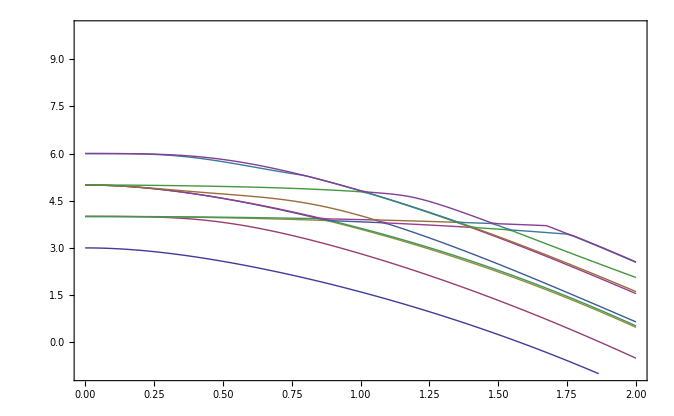

```mathematica
ListPlot[Table[Data[i],{i,1,10,1}],Joined->True,PlotRange->{{α0Min,α0Max},{-1,10}},Frame->True]
```

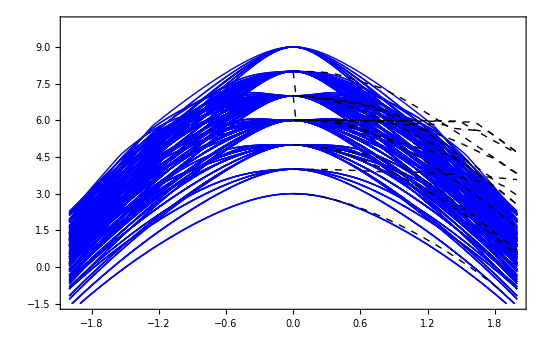

```mathematica
Show[ListPlot[Table[Data2[x],{x,1,counter}],Joined->True,PlotRange->{{αMin,αMax},{-1.5,10}},Frame->True,PlotStyle->Directive[Blue,Thin]],ListPlot[Table[Data[i],{i,1,nEigValues,2}],Joined->True,PlotRange->{{αMin,αMax},{-1,10}},Frame->True,PlotStyle->Directive[Dashed,Black,Thick]]]
```

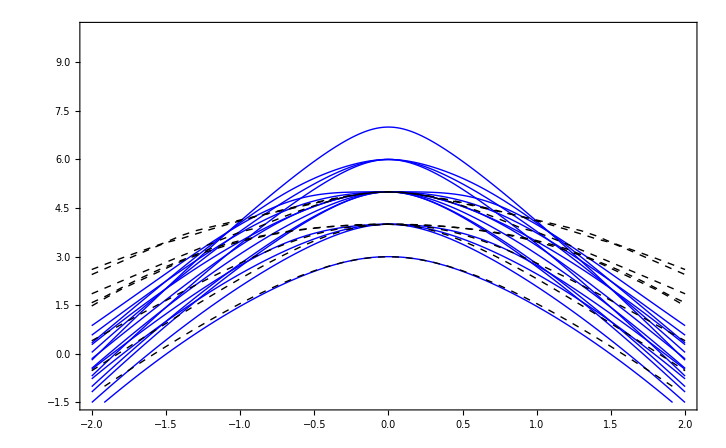

-Graphics-